# Interferometer

## Funktionen

### Includes

```mathematica
Needs["ErrorBarPlots`"]
```

### Fehlerfunktion(Größtfehler) ∑(|df/dx_i|Δx_i)

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
```

### Gaussfunktion

```mathematica
Gauss[a_]:={Mean[a],StandardDeviation[a]/(√Length[a])}
```

### Basics

```mathematica
fAdd[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a+b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

```mathematica
Fdiv[a1_,da1_,b1_,db1_]:= Module[{f,fe,a,b,da,db},
f=a/b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->a1,da->da1,b-> b1,db->db1}]
```

```mathematica
Fmult[γ_,dγ_,δ_,dδ_]:= Module[{f,fe,a,b,da,db},
f=a*b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->γ,da->dγ,b-> δ,db->dδ}]
```

```mathematica
Ff[a1_,da1_,b1_,db1_,c1_,dc1_]:= Module[{f,fe,a,b,c,da,db,dc},
f=a*b/c;
fe = GError[f,{a,b,c},{da,db,dc}];
{f,fe}/.{a->a1,da->da1,b-> b1,db->db1,c->c1,dc->dc1}]
```

## 2.2.) Kalibrierung des Kompensators

```mathematica
λ = 589*10^-9;
nL = 1.0002926;
```

```mathematica
dt={{-0.16, 0}, {0.15, 1}, {0.43, 2}, {0.74, 3}, {1.04, 4}, {1.34, 5}, {1.64, 6}, {1.93, 7}, {2.23, 8}, {2.52, 9}, {2.81, 10}, {3.10, 11}};
```

```mathematica
dn = 1;
dx = 0.01;
```

```mathematica
(*ddt = Table[{dt[[x,1]]*0.01+0.001,dt[[x,2]]*0.015+0.01},{x,1,Length[dt]-2}];*)
```

```mathematica
(*p1 = Table[{{dt[[x,1]],dt[[x,2]]},ErrorBar[ddt[[x,1]],ddt[[x,2]]]},{x,1,Length[dt]}]*)
```

```mathematica
(*ErrorListPlot[p1,Joined-> True,AxesOrigin-> {0,0},AxesLabel-> {"U/V","I/mA"},PlotRange->{{0,0.8},{0,140}}]*)
```

```mathematica
pf1=LinearModelFit[dt,x,x]
```

FittedModel[0.508906+3.37046 x]

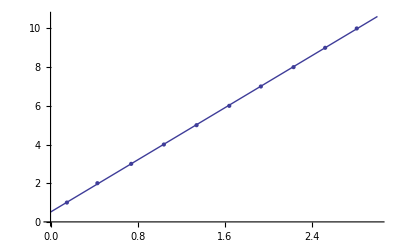

```mathematica
Show[Plot[pf1[x],{x,0,3}],ListPlot[dt],AxesOrigin-> {0,0}]
```

```mathematica
pf1["ParameterTable"]
para1 = pf1["ParameterTableEntries"];
```

| Estimate | Standard Error | t Statistic | P-Value
1 | 0.508906 | 0.0144524 | 35.2127 | 8.09323×10^-12
x | 3.37046 | 0.00802685 | 419.899 | 1.44392×10^-22

```mathematica
β=para1[[2,1]];
```

## 2.4)

```mathematica
w0 =-0.72;
wN =2.06;
N2 = β(wN-w0)
dN = para1[[2,2]];
```

9.36989

```mathematica
n2 = nL + N2*λ
```

1.0003

```mathematica
dn2 =λ*dN
```

4.72781×10^-9